```mathematica
param={v0->1,α0->1,m->0.1,k->1,g->9.8};
eq1=m ξ''[t]+k ξ'[t];
eq2=m y''[t]+k y'[t]+m g;
sol1=NDSolve[{m ξ''[t]+k ξ'[t]==0,ξ[0]==0,ξ'[0]==v0 Cos[α0]}/.param,ξ[t],{t,0,1}];
sol2=NDSolve[{m y''[t]+k y '[t]+m g==0,y[0]==0,y'[0]==v0 Sin[α0]}/.param,y[t],{t,0,1}];
```

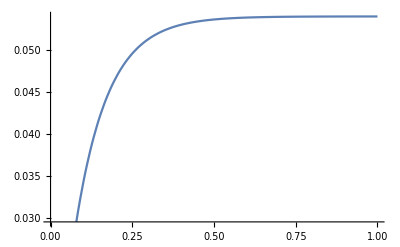

```mathematica
Plot[Evaluate[ξ[t]/.sol1],{t,0,1}]
```

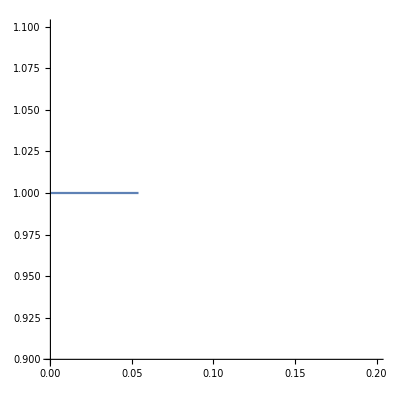

```mathematica
ParametricPlot[Evaluate[{ξ[t],1}/.sol1],{t,0,1},PlotRange->{{0,0.2},{0.9,1.1}}]
```

```mathematica
ξ[t]/.sol1
```

{InterpolatingFunction[…][t]}

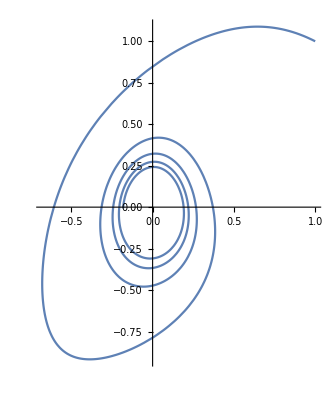

```mathematica
s=NDSolve[{x'[t]==-y[t]-x[t]^2,y'[t]==2x[t]-y[t]^3,x[0]==y[0]==1},{x,y},{t,20}];
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,20}]
```

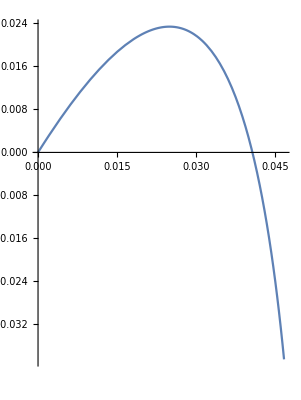

```mathematica
sol3=NDSolve[{m ξ''[t]+k ξ'[t]==0,m y''[t]+k y '[t]+m g==0,ξ[0]==0,ξ'[0]==v0 Cos[α0],y[0]==0,y'[0]==v0 Sin[α0]}/.param,{ξ,y},{t,0,1}];
ParametricPlot[Evaluate[{ξ[t],y[t]}/.sol3],{t,0,0.2}]
```